# 🐺|\[MathematicaIcon] system

#### or how to make an iterative geometry generator

made by Samuel, Gabriel , Théodore and Simon

## Inspirations

### L-system ( or Lindenmayer system)

System with substitution rules like

```mathematica
Axiomes -> "A"
Rules :
"A" -> "AB"
"B" -> "A"
```

```mathematica
1 "A"
2 "AB"
3 "ABA"
4 "ABAAB"
5 "ABAABABA"
```

-Graphics--Graphics-

### Another engine for tiling generation

```mathematica
"Starter tile"
(0,6)
"Rules"
"Append squares to hexagons"
(0,6),1 += (0,4)
(0,6),2 += (0,4)
(0,6),3 += (0,4)
(0,6),4 += (0,4)
"Append hexagon to opposite edge of a square"
(0,4),2 += (0,6)
"Append triangles to square from sides"
(0,4),1 += (0,3)
(0,4),3 += (0,3)
```

#### -Graphics-

### CellPond

-Graphics-

## Famous results

### Sierpiński triangle

### Koch snowflake

```mathematica
systemManipulate[
	{
		{} -> {poly->6, coef->1/3}
	},
	{poly->6, color->Red, nbEdges->6},
	{n, 0, 6}
]
```

### Sierpiński carpet

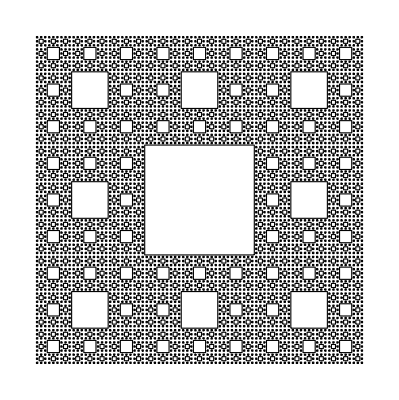

```mathematica
f = And @@ ({poly->4, offset->#, coef->1/3, nbEdges->4}& /@ {{0, Sqrt[2]}, {3*Sqrt[2], Sqrt[2]}});
system[
{
{}->f
},
{poly->4, color->White, nbEdges->4, border->Black},
4
] // Graphics
```

### K-Uniform Tiling

```mathematica
(*4-uniform tilings*)
animsystem[{
{poly-> 3, color -> Yellow, edge -> {1,2,3}} -> {poly -> 4, color -> Red, coef -> 1/0.811},
{poly -> 4, color -> Red, edge -> {1,3}}-> {poly -> 3, color -> Blue, coef -> 0.811},
{poly -> 4, color -> Red, edge -> {2}}-> {poly -> 4, color -> Green, coef -> 1},
{poly -> 4, color -> Green, edge -> {1,3}} -> {poly -> 6, color -> Orange, coef -> 1.4},
{poly -> 4, color -> Green, edge -> {2}} -> {poly -> 4, color -> Gray, coef -> 1},
{poly -> 4, color -> Gray, edge -> {2}}-> {poly -> 3, color -> Yellow , coef -> 0.811},
{poly -> 4, color -> Gray, edge -> {1,3}} -> {poly -> 3, color -> Blue, coef -> 0.811},
{poly -> 6, color -> Orange, edge -> {3}} -> {poly -> 6, color -> Hue[0.9], coef -> 1}
},
{poly -> 3, nbEdges -> 3, color -> Yellow , border -> Black},15, FrameRate -> 3]
```

```mathematica
(**)
```

```mathematica
(**)
animsystem[{
{poly -> 4, color -> Hue[0.6]}-> {poly -> 3, color ->Hue[0.15], coef -> 0.811},
{poly -> 3, color -> Hue[0.15], edge -> 1} -> {poly -> 3, color -> Hue[0.1], coef ->1},
{poly -> 3, color -> Hue[0.15], edge -> 2} -> {poly -> 4, color -> Red, coef -> 1.225},
{poly -> 3, color ->Hue[0.1], edge -> 2} -> {poly -> 3, color -> Hue[0.16], coef -> 1},
{poly -> 3, color -> Hue[0.16], edge -> 1} -> {poly -> 4, color -> Hue[0.59], coef -> 1.225},
{poly -> 4, color -> Hue[0.59]} -> {poly -> 3, color -> Hue[0.145], coef -> 0.811},
{poly -> 3, color -> Hue[0.145], edge -> 2} -> {poly -> 3, color -> Hue[0.11], coef -> 1},
{poly -> 3, color -> Hue[0.11],edge -> 1} -> {poly -> 3, color -> Hue[.147], coef ->1},
{poly -> 3, color -> Hue[.147],edge -> 2} -> {poly -> 4, color -> Hue[0.6], coef ->1.225}
},
{poly -> 4, nbEdges -> 4, angle -> Pi/6, color -> Hue[0.6], border -> Black},20, FrameRate -> 4]
```

## Explaining the code

### The global architecture :

-Graphics-

### Basic rules and their matching

```mathematica
system["Rules","Starting Polygon","Number of Iterations"]
{poly -> 3} -> -Graphics-
{poly -> 4, color -> Blue} -> -Graphics-
{poly -> 5, color -> Yellow, border -> Black} -> -Graphics-
{poly -> 6, color -> Blue} -> {poly -> 3, color -> Red} -> -Graphics-
{poly -> 4, edge -> 2} -> {poly -> 4, color -> Blue, border -> Black, coef -> 0.5} -> -Graphics-
```

### Transformers and the maths behind the geometry

```mathematica
(* the color transformer *)
colorierT[c_, t_] := place |-> With[
	{res=t[place], color=c[place]},
	{Prepend[res[[1]], color], res[[2]] // Map[Append["color"->color]]}
];
```

### Matching of polygon

-Graphics-

## Some Features

### Koch snowflake

```mathematica
systemManipulate[
{
{} -> {poly->6, coef->1/3}
},
{poly->6, color->Red, nbEdges->6},
{n, 0, 6}
]
```

### Graphics Options

```mathematica
Manipulate[
 system[
   {
    {} -> {poly -> 3, offset -> {0,  0.5}, coef -> 1/2, nbEdges -> 3, 
      angle -> Pi, texture -> CurrentImage[]}
    },
   {poly -> 3, color -> Black, nbEdges -> 0, angle -> Pi} && {poly -> 3, 
     nbEdges -> 3, border -> White, coef -> 1/4, 
     offset -> {0, 1/2}, texture -> CurrentImage[]},
   n
   ] // Graphics,
 {n, 0, 6, 1}
 ]
```

### Random

```mathematica
animsystem[{ 
{proba->0.7}->{poly->(RandomInteger[{3,9}]&),color->(RandomColor[]&),offset->({RandomReal[{0,5}],RandomReal[{0,5}]}&),coef->(RandomReal[{0.5,1.5}]&)}},
{poly->9,nbEdges->9},5,FrameRate->0.5]
```

### Evolver, fonction and variables in rules

```mathematica
animsystem[
{
	{edge -> 1}->{poly -> 4, color->(Hue[#i]&), evolver->(<|"i"->#i-0.004|>&), coef->0.995, angle -> Pi/N[Sqrt[53]]}
},
	{poly -> 4, color -> Hue[1], nbEdges -> 6, addvar -> <|"i" -> 1.0|>, coef -> 1},
500
]
```

## Conclusion, Perspective && Thanks